Last modified on: Tuesday, July 10, 2018 at 21:57

Author Info

Kyle Connelly

Carlo Barbieri

North Carolina State University

Poster Session Content

Describing Time Series Data

The goal of this project is to come up with a natural language description of time series data. Given time series data, this algorithm will extract relevant semantic information, and generate a high-level description of the data in natural language.

I first reduced the amount of data to analyze by fitting a sum of piecewise polynomials with local support to the raw data. I then came up with a “fuzzy classification” of the heights of the peaks, and used this description to segment the fit into features, such as flat sections, fast growth, etc. Finally, I used some simple pattern matching and replacement rules to turn this “semantic information” into words describing the graph.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

I successfully set up a system to generate semantic information describing the general structure of time series data. This method can accurately describe local features and global trends, as well as the relative significance of each. My algorithm can describe a dataset of 2000 points in around 500ms. I have also implemented a simple system for converting this semantic information into descriptive words.

The system for going from semantic information to words is very simplistic, and could be greatly improved. Additionally, a system for iteratively more detailed fitting could allow for a more detailed description without over-fitting.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Fit

The data was fit with a sum of piecewise polynomials, each with nonzero values over a local region of the domain. This way the data can be roughly represented by the coefficients of these polynomials.

-Graphics-

“Fuzzy Classification”

This is an idea borrowed from “fuzzy set theory”. Each label has a “classification function”, which indicates how much a certain element belongs to that set. This allows my system to be robust to noise, and to segment data contextually.

-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

The algorithm first subtracts from the data the linear least squares fit, to measure global trends. It then fits this “de-trended” data with a weighted sum of b-spline basis functions, evenly spaced along the x-axis, which have local support and can thus model local features well. The number of b-spline basis functions used can be tweaked by the user to get a more or less detailed description. 

Once the coefficients of these functions are obtained, they are classified into one of seven bins, “big positive”, “medium positive”, “small positive”, “near zero”, ... , “big negative”. This classification is done in the style of fuzzy set theory, where each bin has a “membership function”, which assigns to each coefficient a number from 0 to 1, indicating how much the coefficient belongs in that set. The boundaries of these functions overlap, so one coefficient might belong to “medium positive” with a value of 1, but also to “big positive” with a value less than 1. This sort of “fuzzy classification” mirrors how humans describe similar situations; there is no cutoff value where a number stops being small and becomes big. Practically, this allows the system to be robust to noise, as any noise will not affect classification much. It also allows for context-dependent segmentation of the data; if one coefficient is “medium positive” with value 1, and “big positive” with value less than one, if it is near other “big positive” values it may be interpreted similarly. 

The next step is to calculate a “fuzzy derivative” over these classifications. This is essentially a weighted sum, which returns sort of an “average value” of how much the function increased from one point to another. This is where the context-dependence kicks in. Once this is calculated, the program segments the data into stretches based on sudden changes in this fuzzy derivative. Each of these segments represents a stretch of roughly constant activity, whether that’s a flat section, a sharp increase or decrease, etc. 

These segments are then classified (definitively) as either “sharply increasing”, “increasing”, “flat”, “decreasing”, or “sharply decreasing”. This is represented by an integer from -2 to 2. The number of splines belonging to that segment is also recorded as the relative length of that segment. Additionally, the program records the ratio of increase in the linear fit model, to the largest local fluctuation. This ratio ranks the importance of local to global structure in the data. 

This is the “semantic information” that the algorithm extracts from the data, and represents numerically how a human might describe the data. The next step would then be to turn that information into words. I didn’t put as much time and energy into this part of the project, but some simple pattern matching can be used to change sequences of “up, down, up, down, ...” into “oscillations”, “peaks”, and “valleys”. The rest of the info is then replaced with phrases such as “brief period of fast growth”, “period of slow decline”, etc. Certainly it wouldn’t be very difficult to take this information and stitch it into a better, more natural sounding sentence.

#### Code

Here

#### Conclusions in Detail

The semantic information obtained from this method is robust to noise, and is a good indicator of how a human might describe a plot of the data. It distinguishes local and global features, and can be made into a proper sounding sentence with a sequence of replacement rules and grammatical operations. This scheme is also fast, analyzing sets of 2000 data points in around 500 ms.

#### All Visualizations

```mathematica
base[center_, support_, x_] := BSplineBasis[3, (1/support)*(x-center) + 1/2];
Manipulate[
Plot[1.5*base[center, support, x], {x, -3, 3}],
{{center,0}, -3, 3}, 
{{support, 1}, .25, 6}
]
```

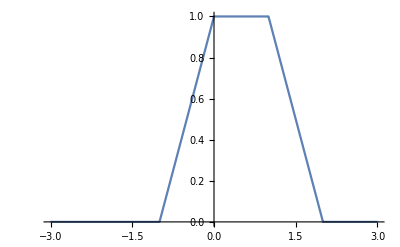

```mathematica
membership[x_, width_] := Ramp[x/width + 1] - UnitStep[x]Ramp[x/width] - UnitStep[x-width]Ramp[x/width - 1] + UnitStep[x-2width]Ramp[x/width - 2];
Plot[membership[x, width]/.width->1, {x, -3, 3}]
```

#### Future Directions

The semantic information obtained by this method does mirror the structure of the data well, but the conversion of this information into words could certainly be improved. Using more natural sounding words and stitching the phrases together in a grammatically correct way would greatly improve this program. Additionally, giving some regions a more detailed fit and description would be a great improvement.

#### Keywords

Provide keywords as items

Semantic

Description

Fuzzy set theory